# DMDGP Package

```mathematica
(* Aborting after first error - Put the following two lines at the top of every notebook. *)
(* messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; *)
```

## Auxiliary Routines

```mathematica
GetEdgeWeight::usage="Gets edge weight. 'E' can be a single edge or a list of edges.";
GetEdgeWeight[G_,E_]:=Module[
{i,D={}},
If[Not[FailureQ[PropertyValue[{G,E[[1]]},EdgeWeight]]],
(* E is a list of edges *)
For[i=1,i≤Length[E],i++,AppendTo[D,PropertyValue[{G,E[[i]]},EdgeWeight]]],
(* E is a single edge *)
D=PropertyValue[{G,E},EdgeWeight]
];
Return[D]
];
```

```mathematica
GetEdgeDistanceBounds[G_,E_]:=Module[
{Lij,Uij,Vij},
Vij=PropertyValue[{G,E},"DistanceBounds"];
Return[Vij]
];
LDME[G_,X_]:=Module[
{i,j,k,E,ldme=0,lij,uij,dij},
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{lij,uij}=GetEdgeDistanceBounds[G,E[[k]]];
i=E[[k]][[1]];
j=E[[k]][[2]];
dij=Norm[X[[i]]-X[[j]]];
ldme+=Max[lij-dij,dij-uij,0]^2
];
Return[Sqrt[ldme/Length[E]]]
];
```

#### RMSD

```mathematica
RMSD[X_,Y_]:=Module[
{xc,yc,x,y,U,D,V,rmsd},
(* calculating centers *)
xc=Mean[X];
yc=Mean[Y];
Print[xc];
(* translation *)
x=Table[X[[i]]-xc,{i,Length[X]}];
y=Table[Y[[i]]-yc,{i,Length[Y]}];
(* svd *)
V=Transpose[x].y;
{U,D,V}=SingularValueDecomposition[V];
V=U.Transpose[V];
x=x.V;
rmsd=Norm[x-y,"Frobenius"]/Sqrt[Length[x]];
Return[{rmsd,V,x,y}]
]
```

```mathematica
(* Example: X and Y are 5 x 3 matrix *)
X={{0.814700,0.097500,0.157600},{0.905800,0.278500,0.970600},{0.127000,0.546900,0.957200},{0.913400,0.957500,0.485400},{0.632400,0.964900,0.800300}};
Y={{6.167723,5.509229,5.376972},{5.921716,5.625914,6.161379},{5.265461,5.705450,6.339958},{5.936486,6.432611,5.883000},{5.680966,5.982123,5.893736}};
{MatrixForm[X],MatrixForm[Y]}
{rmsd,Q,x,y}=RMSD[X,Y];
{rmsd,MatrixForm[Q],MatrixForm[x],MatrixForm[y]}
```

{(0.8147 | 0.0975 | 0.1576
0.9058 | 0.2785 | 0.9706
0.127 | 0.5469 | 0.9572
0.9134 | 0.9575 | 0.4854
0.6324 | 0.9649 | 0.8003),(6.16772 | 5.50923 | 5.37697
5.92172 | 5.62591 | 6.16138
5.26546 | 5.70545 | 6.33996
5.93649 | 6.43261 | 5.883
5.68097 | 5.98212 | 5.89374)}

{0.67866,0.56906,0.67422}

{0.190378,(0.956675 | 0.276543 | 0.091089
-0.283739 | 0.955674 | 0.0786132
-0.0653114 | -0.101053 | 0.992735),(0.297687 | -0.360831 | -0.537546
0.280385 | -0.244816 | 0.292075
-0.539953 | -0.202332 | 0.228932
0.126686 | 0.455218 | -0.135529
-0.164806 | 0.35276 | 0.152068),(0.373253 | -0.341836 | -0.554037
0.127246 | -0.225151 | 0.23037
-0.529009 | -0.145615 | 0.408949
0.142016 | 0.581546 | -0.048009
-0.113504 | 0.131058 | -0.037273)}

#### CheckMDGPSolutionQuality

```mathematica
CheckMDGPSolutionQuality[G_,X_]:=Module[
{i,j,k,dij, Dij,numberOfEdges,E,error},
E=EdgeList[G];
numberOfEdges=Length[E];
error=Table[0,{i,numberOfEdges}];
For[k=1,k≤numberOfEdges,k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
dij=GetEdgeWeight[G,i<->j];
Dij=Norm[X[[i]]-X[[j]]];
error[[k]]=Abs[Dij-dij];
];
Print["max(error) = ",Max[error], " mean(error) = ", Mean[error]]
];
```

## Instance Creation

### Source Code

```mathematica
ClearAll[
SetPositionUsingCartesianSystem,
SetPositionUsingHomogeneousCoords,
CalculateProteinAngles,
GenerateRandom3DBackbone,
GenerateRandomMDGP,
GetMatrixDistance,
Plot3DBackbone,
WriteMDGP
];

SetPositionUsingCartesianSystem[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using rotations and translations explicitly;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]) 
*)
Module[
(* declare local variables *)
{a,b,c,i,v,n,R,X,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]Cos[θ[[3]]],d[[3]]Sin[θ[[3]]] ,0}};
(* set remaining positions *)
For[i=4,i≤numberOfAtoms,i++,
{a,b,c}={X[[i-3]],X[[i-2]],X[[i-1]]};
v= d[[i]]* Normalize[b-c]; 
(* normal to the plane abc *)
n=Cross[a-b,c-b];
(* apply plane rotation *)
R=RotationTransform[θ[[i]],n]; (* rotation creation *)
v=R[v]; (* rotation apply *)
(* apply torsion rotation and translation *)
R=RotationTransform[ω[[i]],c-b];
v=R[v]+c;
(* set i-th coordinate *)
X[[i]]=v
];
Return[X]
];

SetPositionUsingHomogeneousCoords::usage="Set the atoms positions using internal coordinate system.";
SetPositionUsingHomogeneousCoords[d_,θ_,ω_]:=
(* Calculates Euclidean coords from distances, planar and dihedral angles using transformation matrices;
   Input parameters;
   d: distances       (d[i] = norm(x[[i]]-x[[i-1]]));            
   θ: planar angles   (θ[i] = angle(x[i],x[i-1],x[i-2]));        
   ω: dihedral angles (ω[i] = angle(x[i],x[i-1],x[i-2],x[i-3]); 
*)
Module[
{B,B1,B2,B3,X,i,di,ct,st,cw,sw,v,numberOfAtoms},
numberOfAtoms=Length[d];
(* atoms positions on Euclidean 3d space *)
X=Table[0,{i,numberOfAtoms},{j,3}];
(* set the position of the three first points *)
{ct,st}={Cos[θ[[3]]],Sin[θ[[3]]]};
X[[{1,2,3}]]={{0,0,0},{-d[[2]],0,0},{-d[[2]]+d[[3]]ct,d[[3]]st ,0}};
(* set first transformation matrices *)
B1=IdentityMatrix[4];
B2={{-1,0,0,-d[[2]]},{0,1,0,0},{0,0,-1,0},{0,0,0,1}};
di=d[[3]];
B3={{-ct,-st,0,-di*ct},{st,-ct,0,di*st},{0,0,1,0},{0,0,0,1}};
(* set remaining coordinates *)
B=B1.B2.B3;
For[i=4,i≤numberOfAtoms,i++,
{ct,st}={Cos[θ[[i]]],Sin[θ[[i]]]};
{cw,sw}={Cos[ω[[i]]],Sin[ω[[i]]]};
di=d[[i]];
(* concatenate transformation matrices *)
B =B.{{-ct,-st,0,-di*ct},{st*cw,-ct*cw,-sw,di*st*cw},{st*sw,-ct*sw,cw,di*st*sw},{0,0,0,1}};
(* apply transformation at origin *)
v =B.{0,0,0,1};
(* update coordinate *)
X[[i]]=v[[{1,2,3}]];
];
Return[X]
];

GenerateRandom3DBackbone[numberOfAtoms_,algorithm_:"HomogeneousCoords",seed_:0]:=
(* Generates a random backbone in tridimensional Euclidean space;
   Input parameters;
   numberOfAtoms: number of 3D Euclidean points to be generated;
   algorithm: algorithm to be applied during coordinates calculation. The options 'are HomogeneousCoords' or 'CartesianSystem';
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on the current time is constructed;
 *)
Module[
(* declare the local variables *)
{d,θ,ω,X,output,ϵ=0.05},
(* set seed *)
If[seed>0,SeedRandom[seed]];
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
d[[1]]=0;
(* plane angles *)
θ=Table[1.91,{i,numberOfAtoms}];
θ[[{1,2}]]={0,0};
(* torsion angles *)
ω=Table[RandomChoice[{60Degree,180Degree,300Degree}]*(1+RandomReal[{-ϵ,ϵ}]),{i,numberOfAtoms}];
ω[[{1,2,3}]]={0,0,0};
(* set the remaining 3d positions *)
Switch[algorithm,
"HomogeneousCoords",X=SetPositionUsingHomogeneousCoords[d,θ,ω],
"CartesianSystem",X=SetPositionUsingCartesianSystem[d,θ,ω],
_,Throw["InvalidAlgorithm:",OptionValue[algorithm]]
];
(* set output *)
<|"Points"->X,"TorsionAngles"->ω,"CovalentBondLengths"->d,"PlaneRotationAngles"->θ|>
];


GetMatrixDistance[x_]:=
(* Calculates the complete distance matrix for all coordinates x[[i]] in the array x. *)
Table[Norm[x[[i]]-x[[j]]],{i,1,Length[x]},{j,1,Length[x]}];

GenerateRandomMDGP[numberOfAtoms_,dijMax_:5.0,dijPrec_:0.0,algorithm_:"DistanceMatrix",seed_:0]:=
(* Generates a random DMDGP instance.; 
   numberOfAtoms: number of 3D Euclidean points to be generated;
   dijMax: all distances greater than dijMax are dropped;      dijPrec: the upper (uij) and lower (lij) constraints boundaries are generated using the formulae lij = (1-dijPrec) and uij = (1+dijPrec); 
   algorithm: defines the method (algorithm) used to calculate the pairwise distances. The options are "DistanceMatrix" and "Nearest";
   seed: integer number used to reproduce random sequence generation. If seed=0 a sequence based on current is constructed;
*)
Module[
(* declare local variables *)
{i,j,k,X,G,D,N,E,dij},
X=GenerateRandom3DBackbone[numberOfAtoms,"HomogeneousCoords",seed];
Switch[algorithm,
(* case DistanceMatrix *)
"DistanceMatrix",
D=DistanceMatrix[X["Points"]];
G=Table[If[And[0<D[[i]][[j]],D[[i]][[j]]≤dijMax],D[[i]][[j]],Infinity],{i,1,numberOfAtoms},{j,1,numberOfAtoms}];
G=WeightedAdjacencyGraph[G],
(* case Nearest *)
"Nearest",
N=Nearest[X["Points"]->Automatic,X["Points"],{All,dtol}, Method-> "Octree"];
E={};
For[i=1,i≤Length[N],i++,
For[j=1,j≤Length[N[[i]]],j++,
k=N[[i]][[j]];
If[k>i,AppendTo[E,i<->k]]
];
];
G=Graph[E];
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
i=E[[k]][[1]];
j=E[[k]][[2]];
PropertyValue[{G,i<->j},EdgeWeight]=EuclideanDistance[X["Points"][[i]],X["Points"][[j]]]
],
(* otherwise *)
_,Throw["InvalidAlgorithm"]
];
(* set distance bounds *)
E=EdgeList[G];
For[k=1,k≤Length[E],k++,
{i=E[[k]][[1]],j=E[[k]][[2]]};
dij=GetEdgeWeight[G,E[[k]]];
If[Abs[i-j]>2,
(* imprecise distance *)
PropertyValue[{G,i<->j},"DistanceBounds"]={(1-dijPrec),(1+dijPrec)}*dij,
(* exact distance *)
PropertyValue[{G,i<->j},"DistanceBounds"]={dij,dij}
];
];
Return[<|"X"->X,"G"->G|>]
];

Plot3DBackbone[X_]:=
(* Plots the points using the coordinates of X["Points"] property *)
Graphics3D[{Line[X["Points"]],{PointSize[Large],Blue,Point[X["Points"]]}}, Axes->True]

CalculateProteinAngles[A_,B_,C_,D_]:=
(* Calculates the protein angles (plane and torsion) considering the 3D points A, B, C and D in that order. *)
Module[
(* Calculate the plane and torsion angles for X4 *)
{nabc, nbcd},
(* centered at C *)
Print["Angle[BCD] =",VectorAngle[B-C,D-C]];
(* centered at B and C *)
{nabc,nbcd} = {Cross[A-B,C-B],Cross[B-C,D-C]};
Print["Angle[ABCD]=",VectorAngle[nabc,nbcd]];
];

CalculateProteinAnglesForAtomAtPosition[X_,i_]:=
(* Calculates the protein angles (plane and torsion) to i-th atom. *)
CalculateProteinAngles[X[[i-3]],X[[i-2]],X[[i-1]],X[[i]]];

IsNaturalOrderValid[G_]:=
(* Checks if the ordering assumption of DMDGP is satisfied by G edges *)
Module[
(* local variables *)
{i,j},
For[i=4,i≤Length[VertexList[G]],i++,
For[j=1,j≤3,j++,If[FailureQ[GetEdgeWeight[G,i<->(i-j)]],Return[False]]];
];
Return[True]
];

CalculatePartialSolutionError[G_,X_,i_]:=
(* Calculates the error (constraints violation) on the substructure X[[1:i]] *)
Module[
(* local variables *)
{eij,j,k,V,Xi,Xj,Dij,Lij,Uij,errorDij},
(* current position *)
Xi=X[[i]];
(* considering only the precedent atoms *)
V= Select[AdjacencyList[G,i],#<i&];
errorDij=0.0;
For[k=1,k≤Length[V],k++,
(* neighbor index *)
j=V[[k]]; 
(* neighbor coordinate *)
Xj=X[[j]];
(* actual distance *)
Dij=EuclideanDistance[Xi,Xj];
(* distance bounds *)
{Lij,Uij}=GetEdgeDistanceBounds[G,i<->j];
(* error Dij *)
eij=Max[(Lij-Dij)/Lij,(Dij-Uij)/Uij];
(* update error *)
If[eij>errorDij,
errorDij=eij;
(*Print["i=",i," j=",j," Lij=",Lij, " Uij=",Uij, " Dij=",Dij," eij=",errorDij];*)
];
];
Return[errorDij]
];

WriteMDGP[M_,fname_]:=
(* Create the files fname.csv and fname_xsol.csv with, respectively, the MDGP constraints given by M["G"] and the associated solution M["X"] *)
Module[{edges,fid,table,eij,i,j,k,X,G,Lij,Uij},
X=M["X"]["Points"];
table=Table[X[[i]][[j]],{i,Length[X]},{j,3}];
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\bioinfo\\instances\\",fname,"_xsol.csv"];
Export[fid,table,TableHeadings->{"x","y","z"}];
G=M["G"];
edges=EdgeList[G];
table=Table[0,{i,Length[edges]},{j,4}];
For[k=1,k≤Length[edges],k++,
eij=edges[[k]];
{i,j}={eij[[1]],eij[[2]]};
{Lij,Uij}=GetEdgeDistanceBounds[G,eij];
table[[k]]={i,j,Lij,Uij}
];
fid=StringJoin["C:\\Users\\Michael\\gitrepos\\github\\bioinfo\\instances\\",fname,".csv"];
Export[fid,table,TableHeadings->{"I","J","L","U"}]
];
```

### Examples

#### Generating Random Backbone

```mathematica
X=GenerateRandom3DBackbone[8,algorithm="HomogeneousCoords"];
Print["X=",X];
Plot3DBackbone[X]
```

X=<|Points→{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.42007,2.19402,1.17562},{-2.01504,3.59759,1.24393},{-1.6134,4.38056,-0.0028052},{-2.09479,3.63776,-1.24586},{-3.61034,3.47103,-1.18265}},TorsionAngles→{0,0,0,5.32709,3.22244,5.15445,1.01144,1.02451},CovalentBondLengths→{0,1.526,1.526,1.526,1.526,1.526,1.526,1.526},PlaneRotationAngles→{0,0,1.91,1.91,1.91,1.91,1.91,1.91}|>

-Graphics3D-

#### Set Position Using Different Coordinate Systems

```mathematica
d=X["CovalentBondLengths"];
t=X["PlaneRotationAngles"];
w=X["TorsionAngles"];
S=SetPositionUsingCartesianSystem[d,t,w];
P=SetPositionUsingHomogeneousCoords[d,t,w];
Print["S=",S];
Print["P=",P];
CalculateProteinAnglesForAtomAtPosition[S,7];
CalculateProteinAnglesForAtomAtPosition[P,7];
```

S={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.42007,2.19402,1.17562},{-2.01504,3.59759,1.24393},{-1.6134,4.38056,-0.0028052},{-2.09479,3.63776,-1.24586},{-3.61034,3.47103,-1.18265}}

P={{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.42007,2.19402,1.17562},{-2.01504,3.59759,1.24393},{-1.6134,4.38056,-0.0028052},{-2.09479,3.63776,-1.24586},{-3.61034,3.47103,-1.18265}}

Angle[BCD] =1.91

Angle[ABCD]=1.01144

Angle[BCD] =1.91

Angle[ABCD]=1.01144

#### Generate Random DMDGP Instance

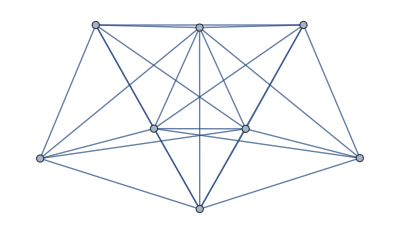
{-Graphics-,-Graphics-,-Graphics3D-}

C:\Users\Michael\gitrepos\github\bioinfo\instances\dmdgp_N8_D5_P0.1_S2.csv

```mathematica
ClearAll[M];
natoms =8;
dijMax=5;
dijPrec=0.1;
seed=2;
M=GenerateRandomMDGP[natoms,dijMax,dijPrec,"DistanceMatrix",seed];{G=M["G"],X=M["X"]};
{G,MatrixPlot[GraphDistanceMatrix[G],ColorFunction->"Monochrome"], Plot3DBackbone[X]}
WriteMDGP[M,StringJoin[{"dmdgp_N",ToString[natoms],"_D",ToString[dijMax],"_P",ToString[dijPrec],"_S",ToString[seed]}]]
```

#### Generate Random IMDGP Instance

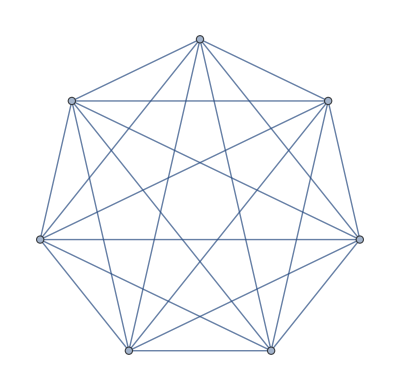
{-Graphics-,-Graphics3D-}

{3.83785,3.83785}

```mathematica
ClearAll[M];
M=GenerateRandomMDGP[7,dtol=5,dprec=0.0,algorithm="DistanceMatrix",seed=1];{G=M["G"],X=M["X"]};
{G, Plot3DBackbone[X]}
{Lij,Uij}=GetEdgeDistanceBounds[G,1<->4]
```

#### Creating Sample

```mathematica
ClearAll[GenerateSample3DBackbone]
GenerateSample3DBackbone[numberOfAtoms_,ω_]:=
Module[{i,k,d,w,θ,X,nvals,nsample,angle,scod,aid},
(* length of covalent bonds *)
d=Table[1.526,{i,numberOfAtoms}];
(* planar angles *)
θ=Table[1.91,{i,numberOfAtoms}];
(* torsion angles *)
w=Table[0,{i,numberOfAtoms}];
nvals=Length[ω];
nsample=nvals^(numberOfAtoms-3);
X=Table[{0,0,0},{i,nsample}];(* coordinates *)
For[k=0,k<nsample,k++,
scod=k; (* sample code *)
For[i=0,i<(numberOfAtoms-3),i++,
aid=Mod[scod,nvals];
scod=(scod-aid)/nvals;
w[[4+i]]=ω[[aid+1]]
];
X[[k+1]]=SetPositionUsingHomogeneousCoords[d,θ,w]
];
Return[X]
];
```

```mathematica
(* Attention: It takes a lot of time!!! *)
X=GenerateSample3DBackbone[8,Table[i*Pi/6,{i,11}]];
Length[X]
```

161051

```mathematica
(* saving structures *)
Export["C:\\Users\\Michael\\gitrepos\\github\\bioinfo\\XCOORDS8.dat",X,"Table"];
```

#### Timing

```mathematica
(* Comparison between HomogeneousCoords and CartesianSystem algorithms *)
(*
Print["Time(HomogeneousCoords)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"HomogeneousCoords"]]]]];
Print["Time(CartesianSystem)=",First[Timing[Timing[GenerateRandom3DBackbone[1000,"CartesianSystem"]]]]];
*)
```

```mathematica
(* Estimating complexity of random backbone generation *)
(*
Clear[x];
tp=Table[{n,First[Timing[GenerateRandom3DBackbone[n,"HomogeneousCoords"]]]},{n,100,10000,100}];
fp=Fit[tp,{1,x},x];
Show[ListPlot[tp],Plot[{fp},{x,100,10000}],AxesLabel->{HoldForm[Problem Size],HoldForm[Time in Seconds]},PlotLabel->HoldForm[GenerateRandom3DBackbone],LabelStyle->{GrayLevel[0]}]
*)
```

```mathematica
(* Estimating complexity of distance calculation algorithms in GenerateRandomMDGP function *)
(*
numberOfAtoms=50
First[Timing[M=GenerateRandomMDGP[numberOfAtoms,Dtol=5.0,algorithm="Nearest"]]]
First[Timing[M=GenerateRandomMDGP[numberOfAtoms,Dtol=5.0,algorithm="DistanceMatrix"]]]
*)
```

## BPSolver

### Source Code

```mathematica
ClearAll[BPPlotEstimatedComplexity];

BPGetNodePosition[G_,X_,i_,branch_]:=
(* Sets X[[i]] considering the graph G, positions X[[j]] for j∈{i-1,i-2,i-3} and branch (0 or 1);
   G: graph with edges information;
   X: list of 3D coordinates;
   i: index of the coordinates to be calculated;
   branch: specifies which of the two branches should be considered;
 *)
Module[
{j,u,v,a,b,c,delta,dy,dz,dw,ky,kz,kw,A,x3,x,y,z,w},
{y,z,w}=Table[X[[i-j]],{j,3}];
{dy,dz,dw}=GetEdgeWeight[G,Table[i<->(i-j),{j,3}]];
(* Print["dy=",dy," dz=",dz," dw=",dw]; *)
{ky,kz,kw}={dy^2-y.y,dz^2-z.z,dw^2-w.w};
(* set x[1:2]=u*x[3]+v *)
A={y[[{1,2}]]-z[[{1,2}]],y[[{1,2}]]-w[[{1,2}]]};
u=LinearSolve[A,{z[[3]]-y[[3]],w[[3]]-y[[3]]}];
v=LinearSolve[A,{(kz-ky)/2,(kw-ky)/2}];
(* set/solve the quadratic equation *)
u={u[[1]],u[[2]],1};v={v[[1]],v[[2]],0};
a=u.u;
b=2*(u.(v-y));
c=v.(v-2*y)-ky;
delta=b^2-4*a*c;
If[delta<0,Return[{Infinity,Infinity,Infinity}]];
(* set the free coordinate avoiding canceling *)
If[b>0,
x3=(-b-Sqrt[delta])/(2*a),
x3=(-b+Sqrt[delta])/(2*a)
];
If[branch==1,x3=(-b/a)-x3];
(* set output *)
x=u*x3+v;
(*Print[y,z,w];
Print["u=",u,"x3=",x3];
Print["a=",a," b=",b," c=",c];
Print["dy=",Norm[x-y]," dz=",Norm[x-z]," dw=",Norm[x-w]];
Print["branch=",branch];*)
Return[x];
];

BPSolver[G_]:=
(* Calculate all solutions of the DMDGP instance defined by the graph G. *)
Module[
(* local variables *)
{i,j,tABC,dAB,dAC,dBC,numberOfAtoms,prune,node,branch,X,S,work,tol=0.001},
numberOfAtoms=Length[VertexList[G]];
(* check if natural order is valid *)
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
(* init atoms positions on Euclidean 3d space *)
X=Table[{0,0,0},{i,numberOfAtoms}];
{dAB,dAC,dBC}=GetEdgeWeight[G,{1<->2,1<->3,2<->3}];
(* planar rotation angle for third atom *)
tABC=ArcCos[(dAB^2+dBC^2-dAC^2)/(2*dAB*dBC)];
(* set the position of the three first points *)
X[[{1,2,3}]]={{0,0,0},{-dAB,0,0},{-dAB+dBC*Cos[tABC],dBC*Sin[tABC] ,0}};
(* init BPTree *)
{branch=Table[0,{i,numberOfAtoms}],branch[[{1,2,3}]]=1};
{node=3,prune=False};
{work=Table[0,{i,numberOfAtoms}],work[[{1,2,3}]]=1};
(* BP core *)
S=<|"Points"->{},"Branches"->{}|>; (* solutions *)
While[True,
(* go to next node *)
If[prune|| node==numberOfAtoms,
(* if pruned or last node, search for a node to branch *)
i=node; prune=False;
While[i>0,If[branch[[i]]==0,branch[[i]]=1;Break[]];i--];
(* stop criterion (there is no next node) *)
If[i==0,Break[]];
(* reset lower (until k) tree levels *)
For[j=i+1,j≤node,j++,branch[[j]]=0];
node=i,
(* if not pruned nor last node, just go to the child node *)
node++
];
(* calculate position of i-th node *)
work[[node]]++;
X[[node]]=BPGetNodePosition[G,X,node,branch[[node]]];
(* prune *)
If[CalculatePartialSolutionError[G,X,node]>tol,prune=True;Continue[]];
(* new solution found *)
If[node==numberOfAtoms,AppendTo[S["Points"],X];AppendTo[S["Branches"],branch]];
];
(*Print["A total of ", Length[S["Points"]]," solutions has been found."];*)
Return[{S,work}]
];

BPPlotEstimatedComplexity[G_]:=
(* Estimates a tight upper bound to the number of solutions given by the connectivity graph G *)
Module[
(* local variables *)
{numberOfAtoms,i,j,k,work,choices,V,R,reduced},
If[Not[IsNaturalOrderValid[G]],Throw["InvalidOrdering"]];
numberOfAtoms=Length[VertexList[G]];
{work=Table[1,{i,numberOfAtoms}],work[[4]]=2};
{choices=Table[Infinity,{i,numberOfAtoms}],choices[[{1,2,3,4}]]={1,1,1,2}};
For[i=5,i≤numberOfAtoms,i++,
(* only edges with precedent vertices *)
V=Select[AdjacencyList[G,i],#<i&];
work[[i]]=2*choices[[i-1]];
If[Length[V]<4,
(* there is no additional constraint *)
choices[[i]]=work[[i]],
(* take the four most restrictive constraints *)
R=Table[choices[[V[[j]]]],{j,Length[V]}];
(* minimal number of choices *)
k=RankedMin[R,4];
(* minimal index with minimal number of choices *)
k=Min[Select[V,(choices[[#]]==k)&]];
(* update intermediate number of choices *)
For[j=(k+1),j≤i,j++,If[choices[[j]]>choices[[k]],choices[[j]]=choices[[k]]]];
];
];
Print["Estimated number of Solutions ",choices[[numberOfAtoms]],"."];
ListLinePlot[work,Filling->Axis, PlotLegends->{"Estimated"}]
];
```

### Examples

```mathematica
M=GenerateRandomMDGP[7,4];
{S,work}=BPSolver[M["G"]]
```

{<|Points→{{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.25391,3.5156,1.35885},{-1.94333,4.16033,2.70664},{-2.54742,5.56098,2.75072}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.25391,3.5156,1.35885},{-1.94333,4.16033,2.70664},{-2.497,5.58217,2.72897}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.25391,3.5156,1.35885},{-1.84761,4.20068,2.66049},{-2.4508,5.60165,2.70669}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.25391,3.5156,1.35885},{-1.84761,4.20068,2.66049},{-2.40216,5.62221,2.68069}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.10928,3.56663,1.29411},{-1.80154,4.21694,2.63986},{-2.26247,5.6715,2.61815}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.10928,3.56663,1.29411},{-1.80154,4.21694,2.63986},{-2.20916,5.68691,2.59851}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.10928,3.56663,1.29411},{-1.70008,4.24616,2.59774},{-2.1602,5.70101,2.57818}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,1.32574},{-2.10928,3.56663,1.29411},{-1.70008,4.24616,2.59774},{-2.10852,5.71584,2.55423}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.25391,3.5156,-1.35885},{-1.94333,4.16033,-2.70664},{-2.54742,5.56098,-2.75072}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.25391,3.5156,-1.35885},{-1.94333,4.16033,-2.70664},{-2.497,5.58217,-2.72897}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.25391,3.5156,-1.35885},{-1.84761,4.20068,-2.66049},{-2.4508,5.60165,-2.70669}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.25391,3.5156,-1.35885},{-1.84761,4.20068,-2.66049},{-2.40216,5.62221,-2.68069}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.10928,3.56663,-1.29411},{-1.80154,4.21694,-2.63986},{-2.26247,5.6715,-2.61815}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.10928,3.56663,-1.29411},{-1.80154,4.21694,-2.63986},{-2.20916,5.68691,-2.59851}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.10928,3.56663,-1.29411},{-1.70008,4.24616,-2.59774},{-2.1602,5.70101,-2.57818}},{{0,0,0},{-1.526,0,0},{-2.03376,1.43905,0},{-1.67489,2.10411,-1.32574},{-2.10928,3.56663,-1.29411},{-1.70008,4.24616,-2.59774},{-2.10852,5.71584,-2.55423}}},Branches→{{1,1,1,0,0,0,0},{1,1,1,0,0,0,1},{1,1,1,0,0,1,0},{1,1,1,0,0,1,1},{1,1,1,0,1,0,0},{1,1,1,0,1,0,1},{1,1,1,0,1,1,0},{1,1,1,0,1,1,1},{1,1,1,1,0,0,0},{1,1,1,1,0,0,1},{1,1,1,1,0,1,0},{1,1,1,1,0,1,1},{1,1,1,1,1,0,0},{1,1,1,1,1,0,1},{1,1,1,1,1,1,0},{1,1,1,1,1,1,1}}|>,{1,1,1,2,4,8,16}}

{0.015625,Null}

{0.015625,Null}

Estimated number of Solutions 16.

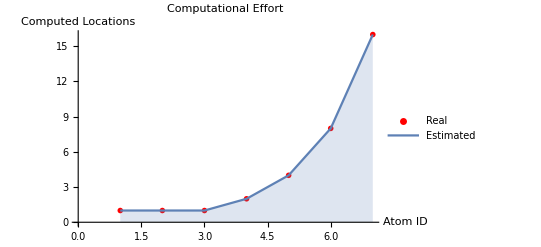

max(error) = 5.9952×10^-15 mean(error) = 1.08062×10^-15

```mathematica
Timing[M=GenerateRandomMDGP[7,4];]
X=M["X"];
G=M["G"];
Timing[{S,work}=BPSolver[G];]
Show[ListPlot[work,PlotStyle->Red,PlotMarkers->{Automatic,Small},PlotLegends->{"Real"}],BPPlotEstimatedComplexity[G],AxesLabel->{HoldForm[Atom ID],HoldForm[Computed Locations]},PlotLabel->HoldForm[Computational Effort]]
CheckMDGPSolutionQuality[G,S["Points"][[1]]]
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"TemperatureMap"] *)
(* MatrixPlot[WeightedAdjacencyMatrix[G],ColorFunction->"Monochrome"] *)
```

## IBPSolver

### Source Code

```mathematica
ClearAll[IBPSolver];
IBPSolver[G_,nslices_:2]:=Module[
{i,k,dij,numberOfAtoms,slices,work,done=False,E,B,Dij,Lij,Uij,S,Z,X,W,isnew},
(* identifying imprecise distances *)
numberOfAtoms=Length[VertexList[G]];
(* branch slices *)
slices=Table[1,{i,numberOfAtoms}];
S=<|"Points"->{},"Branches"->{}|>; (* solutions *)
(* create an work graph (W) *)
E=EdgeList[G];
W=Graph[VertexList[G],E];
For[k=1,k≤Length[E],k++,
PropertyValue[{W,E[[k]]},EdgeWeight]=PropertyValue[{G,E[[k]]},EdgeWeight];
PropertyValue[{W,E[[k]]},"DistanceBounds"]=PropertyValue[{G,E[[k]]},"DistanceBounds"];
];
While[Not[done],
(*Print["slices=",slices];*)
(* generate bp instance *)
For[k=4,k≤numberOfAtoms,k++,
{Lij,Uij}=GetEdgeDistanceBounds[W,(k-3)<->k];
dij=(Uij-Lij)/nslices;
PropertyValue[{W,(k-3)<->k},EdgeWeight]=slices[[k]]*dij+Lij - dij/2;
(*Print["k=",k," Lij=",Lij," Uij=",Uij," Dij=",GetEdgeWeight[W,(k-3)<->k]];*)
];
(* solve bp instance *)
{Z,work}=BPSolver[W];
(* and add new solutions *)
X=Z["Points"];(*Print[X]*);
B=Z["Branches"];
For[k=1,k≤Length[X],k++,
isnew=True;
For[i=1,i≤Length[S["Points"]],i++,
If[Norm[S["Points"][[i]]-X[[k]]]<0.001,isnew=False;Break]
];
If[isnew,
(*Print["branch=",B[[k]]];*)
AppendTo[S["Points"],X[[k]]];
AppendTo[S["Branches"],B[[k]]]
];
];
(* next slice *)
done=True;
For[k=4,k≤numberOfAtoms,k++,
If[slices[[k]]<nslices,
slices[[k]]++;
done=False;
Break[],
(* else *)
slices[[k]]=1
];
];
];
Print["A total of ", Length[S["Points"]]," solutions has been found."];
S
];
```

### Examples

```mathematica
Timing[M=GenerateRandomMDGP[5,4,0.1,algorithm="DistanceMatrix",seed=1];]
X=M["X"];
G=M["G"];
S=IBPSolver[G];
```

{0.,Null}

A total of 8 solutions has been found.

## Artigo

### Problem

```mathematica
vertices={1,2,3,4,5,6};
(* create edges *)
edges={};
For[k=1,k≤(Length[vertices]-1),k++,AppendTo[edges,k<->(k+1)]];
For[k=1,k≤(Length[vertices]-2),k++,AppendTo[edges,k<->(k+2)]];
AppendTo[edges,1<->4];
AppendTo[edges,2<->5];
AppendTo[edges,3<->6];
(* extra distances *)
AppendTo[edges,1<->5];
(* create graph *)
G=Graph[vertices,edges];
(* set edges values *)
For[k=1,k≤(Length[vertices]-1),k++,
PropertyValue[{G,k<->(k+1)},EdgeWeight]=1;
PropertyValue[{G,k<->(k+1)},"DistanceBounds"]={1,1}
]
For[k=1,k≤(Length[vertices]-2),k++,
PropertyValue[{G,k<->(k+2)},EdgeWeight]=Sqrt[3];
PropertyValue[{G,k<->(k+2)},"DistanceBounds"]={Sqrt[3],Sqrt[3]}
]
PropertyValue[{G,1<->4},EdgeWeight]=2.15;
PropertyValue[{G,1<->4},"DistanceBounds"]={2.15,2.15};
PropertyValue[{G,1<->5},EdgeWeight]=0;
PropertyValue[{G,1<->5},"DistanceBounds"]={2.45,2.55};
PropertyValue[{G,2<->5},EdgeWeight]=0;
PropertyValue[{G,2<->5},"DistanceBounds"]={2.2,2.6};
PropertyValue[{G,3<->6},EdgeWeight]=0;
PropertyValue[{G,3<->6},"DistanceBounds"]={2.4,2.6};
(* solving *)
S=IBPSolver[G,8][[1]]
```

A total of 32 solutions has been found.

{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{0.182614,2.42807,0.740936}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.24232,3.24214,0.328392}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{0.182614,2.42807,-0.740936}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.24232,3.24214,-0.328392}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{0.160887,2.45943,0.802441}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.23307,3.25581,0.398864}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{0.160887,2.45943,-0.802441}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.23307,3.25581,-0.398864}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{0.133377,2.4943,0.862971}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.21817,3.26644,0.471673}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{0.133377,2.4943,-0.862971}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.21817,3.26644,-0.471673}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{0.0993544,2.53308,0.922315}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.19689,3.27363,0.547029}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{0.0993544,2.53308,-0.922315}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.19689,3.27363,-0.547029}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{0.0577691,2.57637,0.980168}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.16817,3.27676,0.625235}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{0.0577691,2.57637,-0.980168}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.16817,3.27676,-0.625235}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{0.00703819,2.62509,1.03607}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.13044,3.27493,0.706752}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{0.00703819,2.62509,-1.03607}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.13044,3.27493,-0.706752}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-0.0553999,2.68069,1.08929}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.08113,3.26669,0.792319}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-0.0553999,2.68069,-1.08929}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.08113,3.26669,-0.792319}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-0.134206,2.74583,1.13846}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.779332,2.36788,0.474406},{-1.01558,3.24936,0.883287}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-0.134206,2.74583,-1.13846}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.779332,2.36788,-0.474406},{-1.01558,3.24936,-0.883287}}}

### Getting Starting Points

```mathematica
vertices={1,2,3,4,5,6};
(* create edges *)
edges={};
For[k=1,k≤(Length[vertices]-1),k++,AppendTo[edges,k<->(k+1)]];
For[k=1,k≤(Length[vertices]-2),k++,AppendTo[edges,k<->(k+2)]];
AppendTo[edges,1<->4];
AppendTo[edges,2<->5];
AppendTo[edges,3<->6];
(* extra distances *)
(*AppendTo[edges,1<->5];*)
(* create graph *)
G=Graph[vertices,edges];
(* set edges values *)
For[k=1,k≤(Length[vertices]-1),k++,
PropertyValue[{G,k<->(k+1)},EdgeWeight]=1;
PropertyValue[{G,k<->(k+1)},"DistanceBounds"]={1,1}
]
For[k=1,k≤(Length[vertices]-2),k++,
PropertyValue[{G,k<->(k+2)},EdgeWeight]=Sqrt[3];
PropertyValue[{G,k<->(k+2)},"DistanceBounds"]={Sqrt[3],Sqrt[3]}
]
PropertyValue[{G,1<->4},EdgeWeight]=2.15;
PropertyValue[{G,1<->4},"DistanceBounds"]={2.15,2.15};
PropertyValue[{G,2<->5},EdgeWeight]=2.2;
PropertyValue[{G,2<->5},"DistanceBounds"]={2.2,2.2};
PropertyValue[{G,3<->6},EdgeWeight]=2.4;
PropertyValue[{G,3<->6},"DistanceBounds"]={2.4,2.4};
(* solving *)
S=BPSolver[G][[1]];
```

```mathematica
For[k=1,k≤Length[S["Points"]],k++,
Print["B[",k,"]= ",S["Branches"][[k]]];
Print["X[",k,"]= ",S["Points"][[k]]]
];
```

B[1]= {1,1,1,0,0,0}

X[1]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}}

B[2]= {1,1,1,0,0,1}

X[2]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}}

B[3]= {1,1,1,0,1,0}

X[3]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.40912,1.98082,0.753138},{0.258555,1.66228,1.426}}

B[4]= {1,1,1,0,1,1}

X[4]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.40912,1.98082,0.753138},{-0.265602,2.89149,0.365732}}

B[5]= {1,1,1,1,0,0}

X[5]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-1.50158,1.35009,-1.66303},{-0.758274,1.07521,-2.2729}}

B[6]= {1,1,1,1,0,1}

X[6]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-1.50158,1.35009,-1.66303},{-2.33679,1.69569,-2.0908}}

B[7]= {1,1,1,1,1,0}

X[7]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{0.258555,1.66228,-1.426}}

B[8]= {1,1,1,1,1,1}

X[8]= {{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}

## BuildUpSolver

### Source Code

```mathematica
ClearAll[BuildUpInitX,BuildUpNextBasisAndMatrix,BuildUpSolver]
BuildUpInitX[G_,verbose_:False]:=Module[
{i,j,d,c,absDetA,maxAbsDetA=0,A,C,F,S,U2,U3,U4,V3,V4,X,Y,W},
C=FindClique[G,{4,Infinity},3];
For[i=1,i≤Length[C],i++,
c=Subsets[C[[i]],{4}];
For[j=1,j≤Length[c],j++,
S=c[[j]];
(* set the position of the first four atoms *)
d=Table[GetEdgeWeight[G,S[[i]]->S[[j]]],{i,4},{j,4}];
Y=Table[{0,0,0},{i,4}];
Y[[2]][[1]]=d[[1,2]];U2=Y[[2]][[1]];
Y[[3]][[1]]=(d[[1,3]]^2-d[[2,3]]^2+U2^2)/(2*U2);U3=Y[[3]][[1]];
Y[[3]][[2]]=Sqrt[d[[1,3]]^2-U3^2];V3=Y[[3]][[2]];
Y[[4]][[1]]=(d[[1,4]]^2-d[[2,4]]^2+U2^2)/(2*U2);U4=Y[[4]][[1]];
Y[[4]][[2]]=(d[[2,4]]^2-d[[3,4]]^2-(U4-U2)^2+(U4-U3)^2+V3^2)/(2*V3);V4=Y[[4]][[2]];
Y[[4]][[3]]=Sqrt[d[[1,4]]^2-U4^2-V4^2];
A=Table[Y[[1]]-Y[[j]],{j,2,4}];
absDetA=Abs[Det[A]];
If[absDetA>maxAbsDetA,maxAbsDetA=absDetA;F=S;W=Y];
If[maxAbsDetA>1,Goto[done]]
];
];
Label[done];
If[verbose,Print["Starting basis ", F]];
X=Table[{0,0,0},{i,Length[VertexList[G]]}];
X[[F[[1;;4]]]]=W;
Return[{X,F}];
];

BuildUpNextBasis[G_,F_,U_,X_,verbose_:False]:=Module[
{i,j,k,p,u,basis={},absDetA,maxAbsDetA=0,A,C,P,Y},
For[i=1,i≤Length[U],i++,
u=U[[i]];
P=Subsets[Intersection[AdjacencyList[G,u],F],{4}];
If[Length[P]<1,Continue[]];
For[j=1,j≤Length[P],j++,
p=Permutations[P[[j]]];
For[k=1,k≤Length[p],k++,
Y=Table[X[[p[[k]][[j]]]],{j,4}];
A=2*Table[Y[[1]]-Y[[j]],{j,2,4}];
absDetA=Abs[Det[A]];
(* update basis *)
If[absDetA>maxAbsDetA,
maxAbsDetA=absDetA;
basis=p[[k]];
If[verbose,Print["basis=", basis, " maxAbsDetA=",maxAbsDetA]]
];
If[maxAbsDetA>1,Goto[done]];
];
];
];
Label[done];
If[Length[basis]<1,Throw["BasisCouldNotBeFound"]];
Return[basis];
];

BuildUpSetPosition[G_,X_,S_,basis_]:=Module[
{i,b,d,A,Y,W},
Y=Table[{0,0,0},{i,Length[S]}];
W=Table[X[[basis[[j]]]],{j,4}];
A=2*Table[W[[1]]-W[[j]],{j,2,4}];
A=LUDecomposition[A];
For[i=1,i≤Length[S],i++,
(* get distances *)
d=Table[GetEdgeWeight[G,S[[i]]->basis[[j]]],{j,4}];
b=Table[(Norm[W[[1]]]^2-Norm[W[[j]]]^2)-(d[[1]]^2-d[[j]]^2),{j,2,4}];
Y[[i]]=LUBackSubstitution[A,b]
];
Return[Y]
];

BuildUpSolver[G_,verbose_:False]:=Module[
{i,b,d,basis,A,F,S,U,X,Y},
{X,F}=BuildUpInitX[G,verbose];
(* set remaining atoms *)
U=Complement[Table[j,{j,Length[VertexList[G]]}],F];
While[Length[U]>0,
basis=BuildUpNextBasis[G,F,U,X,verbose];
(* find atoms to set position *)
S=Intersection[AdjacencyList[G,basis[[1]]],U];
S=Intersection[AdjacencyList[G,basis[[2]]],S];
S=Intersection[AdjacencyList[G,basis[[3]]],S];
S=Intersection[AdjacencyList[G,basis[[4]]],S];
If[verbose,Print["F=",F," U=",U," basis=",basis," S=",S]];
(* set positions *)
X[[S]]=BuildUpSetPosition[G,X,S,basis];
F=Union[S,F];
U=Complement[U,S];
];
Return[X]
];
```

### Example

```mathematica
M=GenerateRandomMDGP[5,5,"DistanceMatrix",0];
X=M["X"];
G=M["G"];
S=BuildUpSolver[G];
Print["LDME=",LDME[G,S]]
S
Table[Norm[S[[i]]-S[[5]]]^2,{i,4}]
```

Throw::nocatch: Uncaught Throw[InvalidAlgorithm] returned to top level.

Hold[Throw[InvalidAlgorithm]]

Throw::nocatch: Uncaught Throw[BasisCouldNotBeFound] returned to top level.

Hold[Throw[BasisCouldNotBeFound]]

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 4 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LDME=1/3 √(Max[0,1.526-Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]-√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]+√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]))))],-1.526+Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]-√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]+√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]))))]]^2+Max[0,2.49139-Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]-√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]+√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]))))],-2.49139+Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]-√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]+√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]))))]]^2+Max[0,2.64075-Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]-√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]+√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]))))],-3.22758+Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]-√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]+√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]))))]]^2+(Max[0,1.526-Norm[{{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-3.33679,0.695688,1.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{0.258555,1.66228,1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{-1.2656,1.89149,-0.634268}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-0.758274,1.07521,-2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-3.33679,0.695688,-3.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{0.258555,1.66228,-1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{-1.2656,1.89149,-1.36573}}}],-1.526+Norm[{{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-3.33679,0.695688,1.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{0.258555,1.66228,1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{-1.2656,1.89149,-0.634268}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-0.758274,1.07521,-2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-3.33679,0.695688,-3.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{0.258555,1.66228,-1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{-1.2656,1.89149,-1.36573}}}]])^2+(Max[0,2.49139-Norm[{{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],0.365732-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],-2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],-2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],-1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],-0.365732-Missing[KeyAbsent,3]}}}],-2.49139+Norm[{{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],0.365732-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],-2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],-2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],-1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],-0.365732-Missing[KeyAbsent,3]}}}]])^2+(Max[0,3.45406-Norm[{{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],0.365732-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],-2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],-2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],-1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],-0.365732-Missing[KeyAbsent,4]}}}],-4.22163+Norm[{{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],0.365732-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],-2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],-2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],-1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],-0.365732-Missing[KeyAbsent,4]}}}]])^2+Max[0,1.526-Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,4]],-1.526+Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,4]]]^2+Max[0,2.49139-Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,5]],-2.49139+Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,5]]]^2+Max[0,1.526-Norm[Missing[KeyAbsent,4]-Missing[KeyAbsent,5]],-1.526+Norm[Missing[KeyAbsent,4]-Missing[KeyAbsent,5]]]^2)

<|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.40912,1.98082,0.753138},{0.258555,1.66228,1.426}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-0.40912,1.98082,0.753138},{-0.265602,2.89149,0.365732}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-1.50158,1.35009,-1.66303},{-0.758274,1.07521,-2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-1.50158,1.35009,-1.66303},{-2.33679,1.69569,-2.0908}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{0.258555,1.66228,-1.426}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→{{1,1,1,0,0,0},{1,1,1,0,0,1},{1,1,1,0,1,0},{1,1,1,0,1,1},{1,1,1,1,0,0},{1,1,1,1,0,1},{1,1,1,1,1,0},{1,1,1,1,1,1}}|>

Part::partw: Part 5 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 5 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{(Norm[{{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],0.702375-Missing[KeyAbsent,5]},{-1.50158-Missing[KeyAbsent,5],1.35009-Missing[KeyAbsent,5],1.66303-Missing[KeyAbsent,5]},{-0.758274-Missing[KeyAbsent,5],1.07521-Missing[KeyAbsent,5],2.2729-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],0.702375-Missing[KeyAbsent,5]},{-1.50158-Missing[KeyAbsent,5],1.35009-Missing[KeyAbsent,5],1.66303-Missing[KeyAbsent,5]},{-2.33679-Missing[KeyAbsent,5],1.69569-Missing[KeyAbsent,5],2.0908-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],0.702375-Missing[KeyAbsent,5]},{-0.40912-Missing[KeyAbsent,5],1.98082-Missing[KeyAbsent,5],0.753138-Missing[KeyAbsent,5]},{0.258555-Missing[KeyAbsent,5],1.66228-Missing[KeyAbsent,5],1.426-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],0.702375-Missing[KeyAbsent,5]},{-0.40912-Missing[KeyAbsent,5],1.98082-Missing[KeyAbsent,5],0.753138-Missing[KeyAbsent,5]},{-0.265602-Missing[KeyAbsent,5],2.89149-Missing[KeyAbsent,5],0.365732-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],-0.702375-Missing[KeyAbsent,5]},{-1.50158-Missing[KeyAbsent,5],1.35009-Missing[KeyAbsent,5],-1.66303-Missing[KeyAbsent,5]},{-0.758274-Missing[KeyAbsent,5],1.07521-Missing[KeyAbsent,5],-2.2729-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],-0.702375-Missing[KeyAbsent,5]},{-1.50158-Missing[KeyAbsent,5],1.35009-Missing[KeyAbsent,5],-1.66303-Missing[KeyAbsent,5]},{-2.33679-Missing[KeyAbsent,5],1.69569-Missing[KeyAbsent,5],-2.0908-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],-0.702375-Missing[KeyAbsent,5]},{-0.40912-Missing[KeyAbsent,5],1.98082-Missing[KeyAbsent,5],-0.753138-Missing[KeyAbsent,5]},{0.258555-Missing[KeyAbsent,5],1.66228-Missing[KeyAbsent,5],-1.426-Missing[KeyAbsent,5]}},{{-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1-Missing[KeyAbsent,5],-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-3/2-Missing[KeyAbsent,5],(√3)/2-Missing[KeyAbsent,5],-Missing[KeyAbsent,5]},{-1.31125-Missing[KeyAbsent,5],1.55235-Missing[KeyAbsent,5],-0.702375-Missing[KeyAbsent,5]},{-0.40912-Missing[KeyAbsent,5],1.98082-Missing[KeyAbsent,5],-0.753138-Missing[KeyAbsent,5]},{-0.265602-Missing[KeyAbsent,5],2.89149-Missing[KeyAbsent,5],-0.365732-Missing[KeyAbsent,5]}}}])^2,Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]-√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]+√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]))))]^2,Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,5]]^2,Norm[Missing[KeyAbsent,4]-Missing[KeyAbsent,5]]^2}

## GASolver

### Source Code

#### GASolver

```mathematica
ClearAll[GASolver]
GANextBasis[G_,F_,U_,verbose_:False]:=Module[
{i,u,P,basis},
For[i=1,i≤Length[U],i++,
u=U[[i]];
P=Intersection[AdjacencyList[G,u],F];
If[Length[P]≥4,
basis=Take[P,4];
Return[basis]];
];
Throw["BasisCouldNotBeFound"];
];

GASetPosition[G_,X_,S_,basis_]:=Module[
{i,d,r,w,A,B,C,D,x,y,z,s,u,Y},
Y=Table[{0,0,0},{i,Length[S]}];
(* get basis coords *)
{x,y,z,s}=Table[X[[basis[[j]]]],{j,4}];
For[i=1,i≤Length[S],i++,
u=S[[i]];
(* get distances *)
r=Table[GetEdgeWeight[G,u->basis[[j]]],{j,4}];
(* get factors *) 
w={Sum[x[[j]]^2,{j,3}]-r[[1]]^2,Sum[y[[j]]^2,{j,3}]-r[[2]]^2,Sum[z[[j]]^2,{j,3}]-r[[3]]^2,Sum[s[[j]]^2,{j,3}]-r[[4]]^2};
A=0.5*{(x[[2]]*y[[3]]-x[[3]]*y[[2]])*w[[3]]+(x[[3]]*z[[2]]-x[[2]]*z[[3]])*w[[2]]+(y[[2]]*z[[3]]-y[[3]]*z[[2]])*w[[1]],(x[[3]]*y[[1]]-x[[1]]*y[[3]])*w[[3]]+(x[[1]]*z[[3]]-x[[3]]*z[[1]])*w[[2]]+(y[[3]]*z[[1]]-y[[1]]*z[[3]])*w[[1]],(x[[1]]*y[[2]]-x[[2]]*y[[1]])*w[[3]]+(x[[2]]*z[[1]]-x[[1]]*z[[2]])*w[[2]]+(y[[1]]*z[[2]]-y[[2]]*z[[1]])*w[[1]]};
B={x[[2]]*y[[3]]-x[[2]]*z[[3]]-x[[3]]*y[[2]]+x[[3]]*z[[2]]+y[[2]]*z[[3]]-y[[3]]*z[[2]],x[[3]]*y[[1]]-x[[3]]*z[[1]]-x[[1]]*y[[3]]+x[[1]]*z[[3]]+y[[3]]*z[[1]]-y[[1]]*z[[3]],x[[1]]*y[[2]]-x[[1]]*z[[2]]-x[[2]]*y[[1]]+x[[2]]*z[[1]]+y[[1]]*z[[2]]-y[[2]]*z[[1]]};
C=0.5*{(x[[1]]-z[[1]])*w[[2]]-(x[[1]]-y[[1]])*w[[3]]-(y[[1]]-z[[1]])*w[[1]],(x[[2]]-z[[2]])*w[[2]]-(x[[2]]-y[[2]])*w[[3]]-(y[[2]]-z[[2]])*w[[1]],(x[[3]]-z[[3]])*w[[2]]-(x[[3]]-y[[3]])*w[[3]]-(y[[3]]-z[[3]])*w[[1]]};
d=x[[1]]*y[[2]]*z[[3]]-x[[1]]*y[[3]]*z[[2]]-x[[2]]*y[[1]]*z[[3]]+x[[2]]*y[[3]]*z[[1]]+x[[3]]*y[[1]]*z[[2]]-x[[3]]*y[[2]]*z[[1]];
D={C[[2]]*s[[3]]-C[[3]]*s[[2]]-0.5*B[[1]]*w[[4]]+A[[1]],C[[3]]*s[[1]]-C[[1]]*s[[3]]-0.5*B[[2]]*w[[4]]+A[[2]],C[[1]]*s[[2]]-C[[2]]*s[[1]]-0.5*B[[3]]*w[[4]]+A[[3]],-Dot[A,s]+0.5*d*w[[4]],-Dot[B,s]+d};
Y[[i]]={D[[1]],D[[2]],D[[3]]}/D[[5]]
];
Return[Y]
];

GASolver[G_,verbose_:False]:=Module[
{i,d,x,y,z,r,s,u,w,basis,A,B,C,D,F,S,X,U},
{X,F}=BuildUpInitX[G,verbose];
U=Complement[Table[i,{i,Length[VertexList[G]]}],F];
(*set the remaining atoms*)
While[Length[U]>0,
basis=GANextBasis[G,F,U,verbose];
(* find atoms to set position *)
S=Intersection[AdjacencyList[G,basis[[1]]],U];
S=Intersection[AdjacencyList[G,basis[[2]]],S];
S=Intersection[AdjacencyList[G,basis[[3]]],S];
S=Intersection[AdjacencyList[G,basis[[4]]],S];
If[verbose,Print["F=",F," U=",U," basis=",basis," S=",S]];
X[[S]]=GASetPosition[G,X,S,basis];
F=Union[F,S];
U=Complement[U,S]
];
Return[X]
];
```

#### GASolver2 (Not working)

```mathematica
(*GASolver2[G_]:=Module[
{i,j,d,x,y,z,s,numberOfAtoms,A,C,B,D,Y,M,X,S,U2,U3,U4,V3,V4},
numberOfAtoms=Length[VertexList[G]];
X=Table[{0,0,0},{i,numberOfAtoms}];
(* set the position of the first four atoms *)
X[[2]][[1]]=GetEdgeWeight[G,1->2];U2=X[[2]][[1]];
X[[3]][[1]]=(GetEdgeWeight[G,3->1]^2-GetEdgeWeight[G,3->2]^2+U2^2)/(2*U2);U3=X[[3]][[1]];
X[[3]][[2]]=Sqrt[GetEdgeWeight[G,3->1]^2-U3^2];V3=X[[3]][[2]];
X[[4]][[1]]=(GetEdgeWeight[G,4->1]^2-GetEdgeWeight[G,4->2]^2+U2^2)/(2*U2);U4=X[[4]][[1]];
X[[4]][[2]]=(GetEdgeWeight[G,4->2]^2-GetEdgeWeight[G,4->3]^2-(U4-U2)^2+(U4-U3)^2+V3^2)/(2*V3);V4=X[[4]][[2]];
X[[4]][[3]]=Sqrt[GetEdgeWeight[G,4->1]^2-U4^2-V4^2];
(* set the remaining atoms *)
For[i=5,i≤numberOfAtoms,i++,
P=Select[AdjacencyList[G,i],#<i&];
If[Length[P]<4,Throw["NotEnoughAdjacentNodes"]];
Y=Table[X[[P[[j]]]],{j,4}];
S=Y[[4]];
(* squared distances *)
z=Table[Norm[Y[[j]]]^2-GetEdgeWeight[G,i->P[[j]]]^2,{j,4}];
M=Transpose[{Cross[Y[[2]],Y[[3]]],Cross[Y[[3]],Y[[1]]],Cross[Y[[2]],Y[[1]]]}];
A=0.5*(M.z[[1;;3]]);
B=Table[Sum[M[[k,j]],{j,3}],{k,3}];
C=0.5*(Transpose[{Y[[3]]-Y[[2]],Y[[1]]-Y[[3]],Y[[2]]-Y[[1]]}].z[[1;;3]]);
d =Det[Y[[1;;3]]];Print["Det(A)=",d];
D={C[[2]]*S[[3]]-C[[3]]*S[[2]]-B[[1]]*z[[4]]/2+A[[1]],
C[[3]]*S[[1]]-C[[1]]*S[[3]]-B[[2]]*z[[4]]/2+A[[2]],
C[[1]]*S[[2]]-C[[2]]*S[[1]]-B[[3]]*z[[4]]/2+A[[3]],
-Dot[A,S]+d*z[[4]]/2,
-Dot[B,S]+d};
X[[i]]={D[[1]],D[[2]],D[[3]]}/D[[5]];
];
Return[X]
];*)
```

### Example

```mathematica
M=GenerateRandomMDGP[150,5,"DistanceMatrix",0];
X=M["X"];
G=M["G"];
S=GASolver[G,False];
Print["LDME=",LDME[G,S]]
```

Throw::nocatch: Uncaught Throw[InvalidAlgorithm] returned to top level.

Hold[Throw[InvalidAlgorithm]]

Throw::nocatch: Uncaught Throw[BasisCouldNotBeFound] returned to top level.

Hold[Throw[BasisCouldNotBeFound]]

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 4 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LDME=1/3 √(Max[0,1.526-Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]-√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]+√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]))))],-1.526+Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]-√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,3]]-36 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]+√((-32+36 Conjugate[Missing[KeyAbsent,3]]+36 Missing[KeyAbsent,3]-48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3])^2-4 (48-48 Conjugate[Missing[KeyAbsent,3]]-48 Missing[KeyAbsent,3]+48 Conjugate[Missing[KeyAbsent,3]] Missing[KeyAbsent,3]))))]]^2+Max[0,2.49139-Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]-√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]+√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]))))],-2.49139+Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]-√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,4]]-36 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]+√((-32+36 Conjugate[Missing[KeyAbsent,4]]+36 Missing[KeyAbsent,4]-48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4])^2-4 (48-48 Conjugate[Missing[KeyAbsent,4]]-48 Missing[KeyAbsent,4]+48 Conjugate[Missing[KeyAbsent,4]] Missing[KeyAbsent,4]))))]]^2+Max[0,2.64075-Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]-√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]+√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]))))],-3.22758+Max[√2,1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]-√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])))),1/(√2)(√(32-36 Conjugate[Missing[KeyAbsent,5]]-36 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]+√((-32+36 Conjugate[Missing[KeyAbsent,5]]+36 Missing[KeyAbsent,5]-48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5])^2-4 (48-48 Conjugate[Missing[KeyAbsent,5]]-48 Missing[KeyAbsent,5]+48 Conjugate[Missing[KeyAbsent,5]] Missing[KeyAbsent,5]))))]]^2+(Max[0,1.526-Norm[{{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-3.33679,0.695688,1.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{0.258555,1.66228,1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{-1.2656,1.89149,-0.634268}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-0.758274,1.07521,-2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-3.33679,0.695688,-3.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{0.258555,1.66228,-1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{-1.2656,1.89149,-1.36573}}}],-1.526+Norm[{{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-3.33679,0.695688,1.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{0.258555,1.66228,1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-1.31125,1.55235,0.702375},{-1.40912,0.980819,-0.246862},{-1.2656,1.89149,-0.634268}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-0.758274,1.07521,-2.2729}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.50158,1.35009,-1.66303},{-3.33679,0.695688,-3.0908}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{0.258555,1.66228,-1.426}},{{-1,-1,-1},{-2,-1,-1},{-5/2,-1+(√3)/2,-1},{-2.31125,0.552351,-1.70238},{-1.40912,0.980819,-1.75314},{-1.2656,1.89149,-1.36573}}}]])^2+(Max[0,2.49139-Norm[{{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],0.365732-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],-2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],-2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],-1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],-0.365732-Missing[KeyAbsent,3]}}}],-2.49139+Norm[{{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],0.365732-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-0.758274-Missing[KeyAbsent,3],1.07521-Missing[KeyAbsent,3],-2.2729-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-1.50158-Missing[KeyAbsent,3],1.35009-Missing[KeyAbsent,3],-1.66303-Missing[KeyAbsent,3]},{-2.33679-Missing[KeyAbsent,3],1.69569-Missing[KeyAbsent,3],-2.0908-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{0.258555-Missing[KeyAbsent,3],1.66228-Missing[KeyAbsent,3],-1.426-Missing[KeyAbsent,3]}},{{-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1-Missing[KeyAbsent,3],-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-3/2-Missing[KeyAbsent,3],(√3)/2-Missing[KeyAbsent,3],-Missing[KeyAbsent,3]},{-1.31125-Missing[KeyAbsent,3],1.55235-Missing[KeyAbsent,3],-0.702375-Missing[KeyAbsent,3]},{-0.40912-Missing[KeyAbsent,3],1.98082-Missing[KeyAbsent,3],-0.753138-Missing[KeyAbsent,3]},{-0.265602-Missing[KeyAbsent,3],2.89149-Missing[KeyAbsent,3],-0.365732-Missing[KeyAbsent,3]}}}]])^2+(Max[0,3.45406-Norm[{{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],0.365732-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],-2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],-2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],-1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],-0.365732-Missing[KeyAbsent,4]}}}],-4.22163+Norm[{{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],0.365732-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-0.758274-Missing[KeyAbsent,4],1.07521-Missing[KeyAbsent,4],-2.2729-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-1.50158-Missing[KeyAbsent,4],1.35009-Missing[KeyAbsent,4],-1.66303-Missing[KeyAbsent,4]},{-2.33679-Missing[KeyAbsent,4],1.69569-Missing[KeyAbsent,4],-2.0908-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{0.258555-Missing[KeyAbsent,4],1.66228-Missing[KeyAbsent,4],-1.426-Missing[KeyAbsent,4]}},{{-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1-Missing[KeyAbsent,4],-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-3/2-Missing[KeyAbsent,4],(√3)/2-Missing[KeyAbsent,4],-Missing[KeyAbsent,4]},{-1.31125-Missing[KeyAbsent,4],1.55235-Missing[KeyAbsent,4],-0.702375-Missing[KeyAbsent,4]},{-0.40912-Missing[KeyAbsent,4],1.98082-Missing[KeyAbsent,4],-0.753138-Missing[KeyAbsent,4]},{-0.265602-Missing[KeyAbsent,4],2.89149-Missing[KeyAbsent,4],-0.365732-Missing[KeyAbsent,4]}}}]])^2+Max[0,1.526-Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,4]],-1.526+Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,4]]]^2+Max[0,2.49139-Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,5]],-2.49139+Norm[Missing[KeyAbsent,3]-Missing[KeyAbsent,5]]]^2+Max[0,1.526-Norm[Missing[KeyAbsent,4]-Missing[KeyAbsent,5]],-1.526+Norm[Missing[KeyAbsent,4]-Missing[KeyAbsent,5]]]^2)

## Comparisons

### Speed

```mathematica
M=GenerateRandomMDGP[350,5,"DistanceMatrix",0];
G=M["G"];
Print["GA      = ",Timing[S=GASolver[G,False];]]
Print["BuildUp = ",Timing[Y=BuildUpSolver[G,False];]]
Print["LDME(GA)      = ",LDME[G,S]]
Print["LDME(BuildUp) = ",LDME[G,Y]]
```

Throw::nocatch: Uncaught Throw[InvalidAlgorithm] returned to top level.

Hold[Throw[InvalidAlgorithm]]

Throw::nocatch: Uncaught Throw[BasisCouldNotBeFound] returned to top level.

Hold[Throw[BasisCouldNotBeFound]]

Throw::nocatch: Uncaught Throw[BasisCouldNotBeFound] returned to top level.

Hold[Throw[BasisCouldNotBeFound]]

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

Part::partw: Part 4 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

Norm::nvm: The first Norm argument should be a number, vector, or matrix.

General::stop: Further output of Norm::nvm will be suppressed during this calculation.

Part::partw: Part 3 of <|Points→{{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-0.758274,1.07521,2.2729}},{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,0.702375},{-1.50158,1.35009,1.66303},{-2.33679,1.69569,2.0908}},«5»,{{0,0,0},{-1,0,0},{-3/2,(√3)/2,0},{-1.31125,1.55235,-0.702375},{-0.40912,1.98082,-0.753138},{-0.265602,2.89149,-0.365732}}},Branches→«1»|> does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification Y⟦1⟧ is longer than depth of object.

Part::partd: Part specification Y⟦2⟧ is longer than depth of object.

Part::partd: Part specification Y⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

LDME(BuildUp) = 1/3 √(Max[0,1.526-Norm[Y⟦1⟧-Y⟦2⟧],-1.526+Norm[Y⟦1⟧-Y⟦2⟧]]^2+Max[0,2.49139-Norm[Y⟦1⟧-Y⟦3⟧],-2.49139+Norm[Y⟦1⟧-Y⟦3⟧]]^2+Max[0,1.526-Norm[Y⟦2⟧-Y⟦3⟧],-1.526+Norm[Y⟦2⟧-Y⟦3⟧]]^2+Max[0,3.45406-Norm[Y⟦1⟧-Y⟦4⟧],-4.22163+Norm[Y⟦1⟧-Y⟦4⟧]]^2+Max[0,2.49139-Norm[Y⟦2⟧-Y⟦4⟧],-2.49139+Norm[Y⟦2⟧-Y⟦4⟧]]^2+Max[0,1.526-Norm[Y⟦3⟧-Y⟦4⟧],-1.526+Norm[Y⟦3⟧-Y⟦4⟧]]^2+Max[0,2.64075-Norm[Y⟦2⟧-Y⟦5⟧],-3.22758+Norm[Y⟦2⟧-Y⟦5⟧]]^2+Max[0,2.49139-Norm[Y⟦3⟧-Y⟦5⟧],-2.49139+Norm[Y⟦3⟧-Y⟦5⟧]]^2+Max[0,1.526-Norm[Y⟦4⟧-Y⟦5⟧],-1.526+Norm[Y⟦4⟧-Y⟦5⟧]]^2)

### Robustness

#### Example: Colinear Points

```mathematica
(*z=Table[10^(i),{i,1,16}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0.5,1/z[[k]],0},{1,2,3}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤4,i++,
For[j=i+1,j≤4,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
Z=BPGetNodePosition[G,X,4,{1,1,1,1}];
Print["k= ",k,"  Log10[E]= ", Log10[Norm[X[[4]]-Z]] ]
];*)
```

#### Example B

```mathematica
z=Table[10^(-i),{i,0,12}];
a=Table[0,{i,Length[z]}];
b=Table[0,{i,Length[z]}];
For[k=1,k≤Length[z],k++,
X={{0,0,0},{1,0,0},{0,1,0},{1,1,z[[k]]},{.5,.5,1}};
(* build graph *)
edges={};
weights={};
For[i=1,i≤5,i++,
For[j=i+1,j≤5,j++,
AppendTo[edges,i<->j];
AppendTo[weights,Norm[X[[i]]-X[[j]]]]
];
];
G=Graph[edges,EdgeWeight->weights];
S={5};
basis={1,2,3,4};
a[[k]]=Norm[X[[S]]-BuildUpSetPosition[G,X,S,basis]];
b[[k]]=Norm[X[[S]]-GASetPosition[G,X,S,basis]]
];
```